```mathematica
Remove["Global`*"];
ClearAll["Global`*"];
Get[NotebookDirectory[]<>"QBMMlib.wl"];
Get[NotebookDirectory[]<>"TimeSteppers.wl"];
```

```mathematica
model="nonlinear";
If[model=="linear",
	Ca=1/2;γ=1;Rey=Infinity;
	Cp0=1;
	Cp[t_]:=Cp0;
	Toneperiod=3.4 (1/Cp0)^0.75;
];
If[model=="nonlinear",
	Ca=1/2;γ=1.4;
	Cp0=1/(1-0.1);
	(*Cp0=1/0.5;*)
	Toneperiod=3.4 2  (1/Cp0)^0.75;
	(*Cp[t_]:=Cp0;*)
	Cp[t_]:=If[t<Toneperiod,Cp0 Sin[2 Pi t/Toneperiod]+1,1];
];
Nperiod=1;
T=Nperiod Toneperiod;

dt=1.  10^-5;dt0=dt;
dtmin=dt;dtmax=1000dt;
tol=1 10^-5;

μR=1.;σR=0.1;
μRd=10^-14;σRd=0.1;
μRo=1.;σRo=0.2;
𝒟r=LogNormalDistribution[Log[μR],σR];
𝒟v=NormalDistribution[μRd,σRd];
RRdPDF=ProductDistribution[𝒟r,𝒟v];
(*RRdPDF=BinormalDistribution[{μR,μRd},{σR,σRd},0.1];*)
```

```mathematica
nro=1;
𝒟ro=LogNormalDistribution[Log[μRo],σRo];
momRo[i_]:=Moment[𝒟ro,i];
momRos=Table[momRo[i],{i,0,2nro-1}];
{Ros,wRos}=wheeler[momRos,nro];

momRRd[i_,j_,k_:0]:=Moment[RRdPDF,{i,j}];

method="CQMOM";(*"CQMOM" or "CHyQMOM"*)
nr=2;
nrd=2;
If[method=="CHyQMOM"&&nr==3,qmax=1];

ks=momidx[nr,nrd,method,nro];
ksp={{3,0},{2,1},{3,2},{3(1-γ),0}};
```

```mathematica
frhs[mom_,t_,l_,m_,n_]:=Module[{},
	If[model=="linear",Return[l mom[l-1,m+1,n]-m(mom[l,m,n]+ mom[l+1,m-1,n]-mom[l,m-1,n+1]+Cp[t] mom[l,m-1,n]),Module]];
	(*If[model=="nonlinear",Return[l mom[l-1,m+1,0]+m(mom[l-1-3γ,m-1,0]-3/2 mom[l-1,m+1,0]-Cp[t] mom[l-1,m-1,0]),Module]];*)
	If[model=="nonlinear",Return[l mom[l-1,m+1,n]+m(mom[l-1-3γ,m-1,n+3γ]-3/2 mom[l-1,m+1,n]-Cp[t] mom[l-1,m-1,n]),Module]];
];

myrhs[moms_,t_]:=Module[{mom,rhs,momout,rhs1,rhs2,momsp1,momsp2,momout1,momout2,w},
	If[method=="CHyQMOM",
		{w,xix,xiy}=chyqmom[moms,ks,qmax];
		{momout,momsp,mom}=quad[w,xix,xiy,method,nr,nrd,ks,ksp];
		rhs=Table[frhs[mom,t,ks[[i,1]],ks[[i,2]]],{i,Length[ks]}];
		Return[{momout,rhs},Module];
	];
	If[method=="CQMOM",
		{w,xi,xis}=cqmom12[moms,ks,nr,nrd,nro,wRos,Ros];
		{momout1,momsp1,mom}=quad[w,xi,xis,method,nr,nrd,ks,ksp,12,nro,wRos,Ros];
		rhs1=Table[frhs[mom,t,ks[[i,1]],ks[[i,2]],ks[[i,3]]],{i,Length[ks]}];
		
		{w,xi,xis}=cqmom21[moms,ks,nr,nrd,nro,wRos,Ros];
		{momout2,momsp2,mom}=quad[w,xi,xis,method,nr,nrd,ks,ksp,21,nro,wRos,Ros];
		rhs2=Table[frhs[mom,t,ks[[i,1]],ks[[i,2]],ks[[i,3]]],{i,Length[ks]}];

		momsp=(momsp1+momsp2)/2;
		Return[{(momout1+momout2)/2,(rhs1+rhs2)/2},Module];
	];
];
```

```mathematica
moms=Table[Sum[wRos[[l]] Ros[[l]]^ks[[i,3]] momRRd[ks[[i,1]],ks[[i,2]],l],{l,1,nro}],{i,1,Length[ks]}];
{w,xi,xis}=cqmom12[moms,ks,nr,nrd,nro,wRos,Ros];
{momout1,momsp1,mom}=quad[w,xi,xis,method,nr,nrd,ks,ksp,12,nro,wRos,Ros];
(*rhs1=Table[frhs[mom,t,ks[[i,1]],ks[[i,2]],ks[[i,3]]],{i,Length[ks]}];*)
```

```mathematica
moms=Table[Sum[wRos[[l]] Ros[[l]]^ks[[i,3]] momRRd[ks[[i,1]],ks[[i,2]],l],{l,1,nro}],{i,1,Length[ks]}];
sol={};ts={};dets={};abscissa={};spsol={};t=0;dt=dt0;
Monitor[While[t≤T,
	{moms,mome,e}=RK23[moms,myrhs,t,dt];

	(*If[method=="CHyQMOM",AppendTo[abscissa,Thread[{xix,xiy}]]];
	If[method=="CQMOM",AppendTo[abscissa,Flatten[Table[Thread[{xis[i],xi[[i]]}],{i,1,nrd}],1]]];*)
	AppendTo[sol,moms];AppendTo[spsol,momsp];
	AppendTo[ts,t];

	t=t+dt;
	dt=dt Min[Max[Sqrt[tol/(2 e)],0.3],2.];
dt=Min[Max[0.9 dt,dtmin],dtmax];

If[Norm[moms]>10^8,Print["Crash ",100 t/T];Break[]];
];
,TableForm[{{"Time",100t/T},{"δt",dt/dt0},{"Moments",Max[Abs[moms]]}}]
];
Length[ts]
```

738

```mathematica
myn=100;
plottingfac=1;
myts=Table[ts[[i]],{i,1,Length[abscissa],Floor[Length[abscissa]/myn]}];
myabscissa=Table[abscissa[[i]],{i,1,Length[abscissa],Floor[Length[abscissa]/N[myn]]}];
xdat=myabscissa[[All,All,1]];
ydat=myabscissa[[All,All,2]];
xmax=If[Max[xdat]>0,1.2 Max[xdat],0.8 Max[xdat]];
xmin=If[Min[xdat]<0,1.2 Min[xdat],0.8 Min[xdat]];
ymax=If[Max[ydat]>0,1.2 Max[ydat],0.8 Max[xdat]];
ymin=If[Min[ydat]<0,1.2Min[ydat],0.8 Min[ydat]];
ListAnimate[ParallelTable[
ListPlot[myabscissa[[i]],PlotStyle->Red,PlotRange->{{xmin,xmax},{ymin,ymax}}]
,{i,1,Length[myabscissa]/plottingfac}]]
```

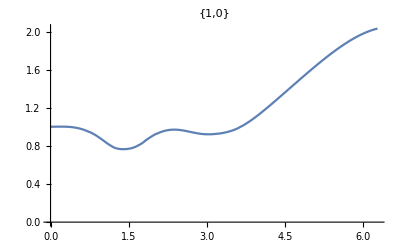
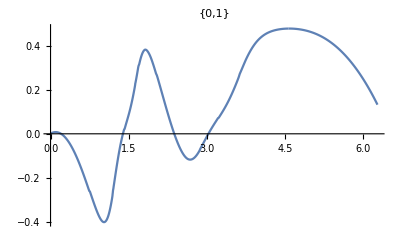
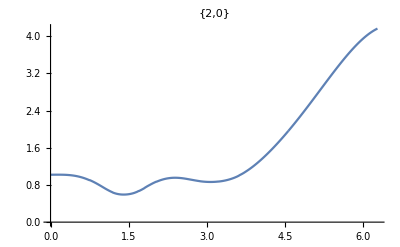
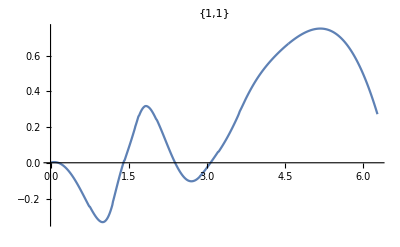
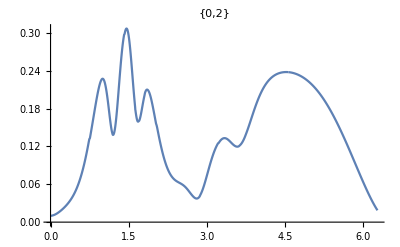
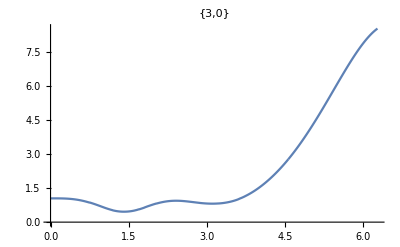
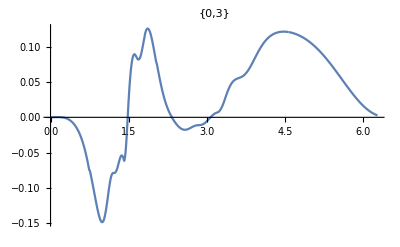
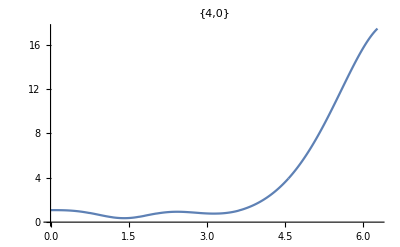

```mathematica
plots={};
Do[
If[Total[ks[[i]]]<10&&Total[ks[[i]]]>0,
AppendTo[plots,ListPlot[Thread[{ts,sol[[All,i]]}],Joined->True,PlotRange->All,PlotLabel->ks[[i]]]]
]
,{i,1,Length[moms]}]
plots
```

```mathematica
(* Verify with Monte Carlo *)
Ncases=1000;
cases=RandomVariate[RRdPDF,Ncases];
type="nonlinear";
Clear[t];
If[type=="linear",
	β=2/Rey;ω2= 2 γ Ca;
	myr=ParallelTable[
	r[t]/.(NDSolve[
{r''[t] == -2 β r'[t]-ω2 r[t]-Cp[t],r[0]==cases[[i,1]],r'[0]==cases[[i,2]]},
r[t],
{t,0,T}]//First//First),
{i,1,Ncases}];
,
	myr=ParallelTable[
r[t]/.(NDSolve[
{r[t]r''[t]+3/2 r'[t]^2 ==(1/r[t])^(3 γ)-Cp[t],r[0]==cases[[i,1]],r'[0]==cases[[i,2]]},
r[t],
{t,0,T}]//First//First),
{i,1,Ncases}];
];
mydr=ParallelTable[
D[myr[[i]],t],{i,1,Ncases}];

Nt=100;ts2=Table[i,{i,0,T,T/Nt}];
ts2=myts;Nt=Length[ts2];
P=Table[Table[{
myr[[j]]/.{t->ts2[[i]]},
mydr[[j]]/.{t->ts2[[i]]}},{j,1,Ncases}],
{i,1,Nt}];

mcmoms=ParallelTable[Table[{ts2[[i]],Moment[P[[i]],ks[[j,1;;2]]]},{i,1,Nt}],{j,1,Length[ks]}];
mcmomssp=ParallelTable[Table[{ts2[[i]],Moment[P[[i]],ksp[[j,1;;2]]]},{i,1,Nt}],{j,1,Length[ksp]}];
```

```mathematica
plts=ParallelTable[
Show[
DensityHistogram[P[[i]],PlotRange->{{xmin,xmax},{ymin,ymax},All}],
ListPlot[myabscissa[[i]],PlotStyle->Red,PlotRange->{{xmin,xmax},{ymin,ymax}}]]
,{i,1,Length[P]/1}];
vid=ListAnimate[plts]
```

```mathematica
(*Export["~/Desktop/movie.avi",vid]*)
```

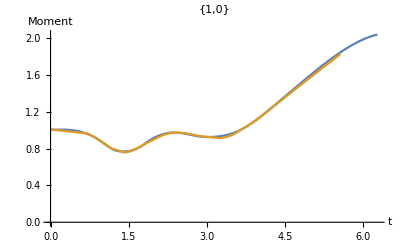
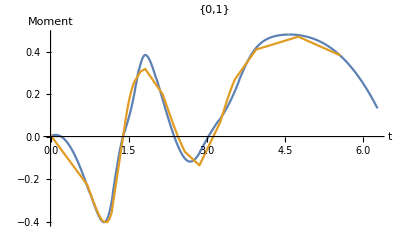
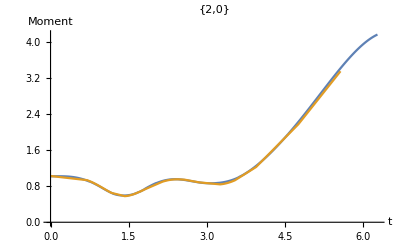
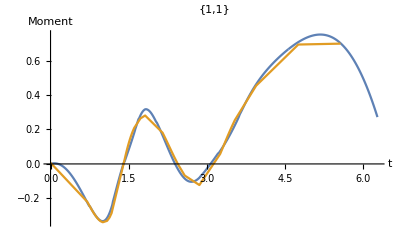
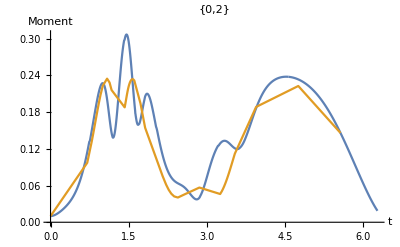
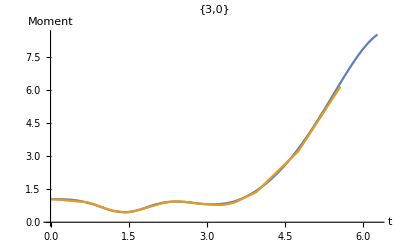
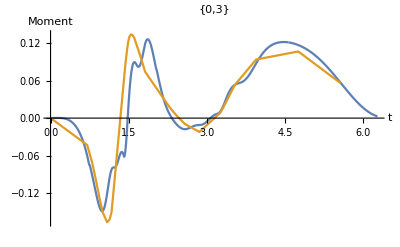
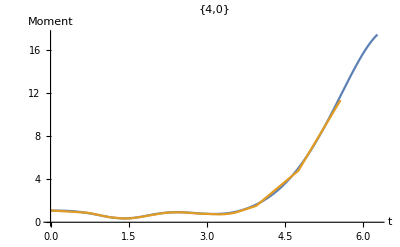

```mathematica
plots={};
Do[
If[Total[ks[[i]]]<10&&Total[ks[[i]]]>0,
AppendTo[plots,ListPlot[{Thread[{ts,sol[[All,i]]}],mcmoms[[i]]},Joined->True,PlotRange->All,PlotLabel->ks[[i]],AxesLabel->{"t","Moment"}]]
]
,{i,1,Length[moms]}]
plots

plots={};
Do[
AppendTo[plots,ListPlot[{Thread[{ts,spsol[[All,i]]}],mcmomssp[[i]]},Joined->True,PlotRange->All,PlotLabel->ksp[[i]],AxesLabel->{"t","Moment"}]]
,{i,1,Length[momsp]}]
plots
```